{t,H,P}

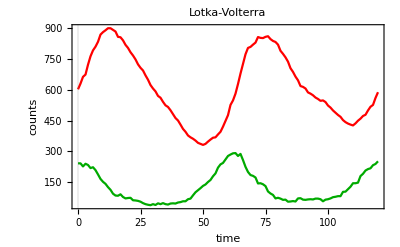

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["../data_lotka_volterra_gillespie/000.txt","Table"];
header=data[[1]]
dataTime=data[[2;;,1]];
dataHunter=data[[2;;,2]];
dataPrey=data[[2;;,3]];

leg=LineLegend[{Darker[Green],Red},{"Prey","Hunter"},LabelStyle->Directive[FontSize->24]];

plt=Row[{
Show[
ListLinePlot[Transpose[{dataTime,dataHunter}],PlotStyle->Red],
ListLinePlot[Transpose[{dataTime,dataPrey}],PlotStyle->Darker[Green]],
FrameLabel->{"time","counts"},
PlotLabel->"Lotka-Volterra",
PlotRange->All
],leg
}]
```

```mathematica
Export["figure_lotka_volterra.jpg",plt,ImageResolution->200]
```

figure_lotka_volterra.jpg

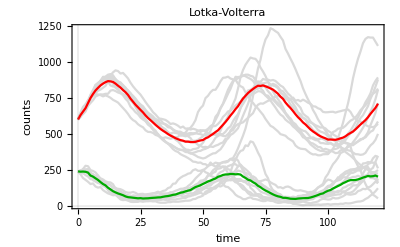

```mathematica
SetDirectory[NotebookDirectory[]];

plts={};
dataHunterSt={};
dataPreySt={};

Do[
data=Import["../data_lotka_volterra_gillespie/"<>IntegerString[seed,10,3]<>".txt","Table"];
dataTime=data[[2;;,1]];
dataHunter=data[[2;;,2]];
dataPrey=data[[2;;,3]];

AppendTo[plts,ListLinePlot[Transpose[{dataTime,dataHunter}],PlotStyle->LightGray]];
AppendTo[plts,ListLinePlot[Transpose[{dataTime,dataPrey}],PlotStyle->LightGray]];

AppendTo[dataHunterSt,dataHunter];
AppendTo[dataPreySt,dataPrey];
,{seed,0,9}]

leg=LineLegend[{Darker[Green],Red},{"Prey","Hunter"},LabelStyle->Directive[FontSize->24]];

Row[{
Show[
plts,
ListLinePlot[Transpose[{dataTime,Mean[dataHunterSt]}],PlotStyle->Red],
ListLinePlot[Transpose[{dataTime,Mean[dataPreySt]}],PlotStyle->Darker[Green]],
PlotRange->All,
FrameLabel->{"time","counts"},
PlotLabel->"Lotka-Volterra"
],leg}]
```

```mathematica
Export["figure_lotka_volterra_ave.jpg",plt,ImageResolution->200]
```

figure_lotka_volterra_ave.jpg